```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
PNGtoGray[filename_]:=Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
GIFtoGray[filename_]:=255-Reverse[Map[Map[First,#]&,Import[filename,"Data"]]];
showBinaryImage[bimg_]:=Graphics[Raster[bimg],Frame->False];
showGrayImage[img_]:=Graphics[Raster[img/Max[img]],Frame->False];
traceFace[edgelist_]:=Module[{face=edgelist⟦1⟧,p,nlist=Drop[edgelist,1]},
While[Length[nlist]>1,
p=Position[nlist,Last[face]];
AppendTo[face,nlist⟦p⟦1,1⟧,3-p⟦1,2⟧⟧];
nlist=Drop[nlist,{p⟦1,1⟧}]];
face];
getScale[cc_]:=Max[Map[(Max[#]-Min[#]+1)&,Transpose[cc⟦1⟧]]];
getExteriorFaces[cc_]:=Module[{val},
val=Map[0&,cc⟦3⟧];
Scan[Scan[val⟦#⟧++&,#]&,cc⟦4⟧];
Pick[cc⟦3⟧,Map[(#<2)&,val]]];
ptSize2D=0.02;ptColor2D=GrayLevel[0];ptColorOri2D=GrayLevel[0.85];
edgeSize2D=0.01;edgeColor2D=GrayLevel[.2];edgeColorOri2D=GrayLevel[0.9];faceColor2D=GrayLevel[0.5];faceColorOri2D=GrayLevel[0.95];
showCC2D[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics[{
If[len≥3,{faceColor2D,EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{edgeColor2D,Thickness[edgeSize2D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{ptColor2D,PointSize[ptSize2D/scl],Map[Point,cc⟦1⟧]}}]];
showCC2D[cc1_,cc2_]:=Module[{scl=getScale[cc2]/10.0,len1=Length[cc1],len2=Length[cc2]},
Graphics[{
If[len2≥3,{faceColorOri2D,EdgeForm[{}],Map[Polygon[cc2⟦1,traceFace[cc2⟦2,#⟧]⟧]&,cc2⟦3⟧]},{}],
If[len2≥2,{edgeColorOri2D,Thickness[edgeSize2D/scl],Map[Line[cc2⟦1,#⟧]&,cc2⟦2⟧]},{}],
{ptColorOri2D,PointSize[ptSize2D/scl],Map[Point,cc2⟦1⟧]},
If[len1≥3,{faceColor2D,EdgeForm[{}],Map[Polygon[cc1⟦1,traceFace[cc1⟦2,#⟧]⟧]&,cc1⟦3⟧]},{}],
If[len1≥2,{edgeColor2D,Thickness[edgeSize2D/scl],Map[Line[cc1⟦1,#⟧]&,cc1⟦2⟧]},{}],
{ptColor2D,PointSize[ptSize2D/scl],Map[Point,cc1⟦1⟧]}}]];
showCC2DImg[cc_,img_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Show[{showGrayImage[img],Graphics[{
If[len≥3,{RGBColor[1,0,0],EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{RGBColor[1,0,0],Thickness[edgeSize2D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{RGBColor[1,0,0],PointSize[ptSize2D/scl],Map[Point,cc⟦1⟧]}}]}]];
ptSize3D=0.02;ptColor3D=GrayLevel[0];
edgeSize3D=0.01;edgeColor3D=GrayLevel[0];
faceColor3D=GrayLevel[0.5];
opaqe3D=0.2;
showCC3D[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics3D[{
If[len≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,cc⟦3⟧]},{}],
If[len≥2,{edgeColor3D,Thickness[edgeSize3D/scl],Map[Line[cc⟦1,#⟧]&,cc⟦2⟧]},{}],
{ptColor3D,PointSize[ptSize3D/scl],Map[Point,cc⟦1⟧]}},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
showCC3DExt[cc_]:=Module[{scl=getScale[cc]/10.0,len=Length[cc]},
Graphics3D[{
If[len≥3,{faceColor3D,EdgeForm[{edgeColor3D,Thickness[edgeSize3D/scl]}],Map[Polygon[cc⟦1,traceFace[cc⟦2,#⟧]⟧]&,getExteriorFaces[cc]]},{}]},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
showCC3D[cc1_,cc2_]:=Module[{scl=getScale[cc2]/10.0,len1=Length[cc1],len2=Length[cc2]},
Graphics3D[{{Opacity[opaqe3D],
If[len2≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc2⟦1,traceFace[cc2⟦2,#⟧]⟧]&,getExteriorFaces[cc2]]},{}]},
If[len1≥3,{faceColor3D,EdgeForm[{}],Map[Polygon[cc1⟦1,traceFace[cc1⟦2,#⟧]⟧]&,cc1⟦3⟧]},{}],
If[len1≥2,{edgeColor3D,Thickness[edgeSize3D/scl],Map[Line[cc1⟦1,#⟧]&,cc1⟦2⟧]},{}],
{ptColor3D,PointSize[ptSize3D/scl],Map[Point,cc1⟦1⟧]}},
Boxed->False,RotationAction->Clip,Lighting->"Neutral"]];
```

```mathematica
yo=Table[i,{i,3},{j,2}]
```

{{1,1},{2,2},{3,3}}

```mathematica
yo[[0]]
```

List

```mathematica
(*Here we mark the one cells*)

edges={{k,l+1},{k,l+2},{2*i-1,2*j},{2*i-1,2*j-1}};
edgesAre={{1,2},{1,3},{2,4},{3,4}};
(*0-cell process order is {DownLeft,TopLeft,DownRight,TopRight}*)
(*It follows that edges will be 1-2,1-3,2-4,3-4*)
For[i=1,i≤4,i++,
a=edges⟦i⟧⟦1⟧;b=edges⟦i⟧⟦2⟧;
cc⟦2⟧=If[markEdges==True&&usedArr⟦a,b⟧==False,
usedArr⟦k,l⟧=True;
Append[cc⟦2⟧,{k,l}],cc⟦1⟧]
];
markEdges=False;
(*end of marking the one cells*)
```

```mathematica
arrr={{1},{2},{3},{4}}
```

{{1},{2},{3},{4}}

```mathematica
arrr[[Length[arrr]-3]]
```

{1}

```mathematica
(*Here we mark the one cells*)
edges={{2*i-2,2*j-1},{2*i,2*j-1},{2*i-1,2*j},{2*i-1,2*j-2}};
(*Above are left edge, right edge, top edge, down edge, respectively*)
(*Left edge*)
a=edges⟦1⟧⟦1⟧;b=edges⟦1⟧⟦2⟧;
cc⟦2⟧=If[array⟦i,j⟧==1&&usedArr⟦a,b⟧==False,
totalOneCells+=1;
usedArr⟦a,b⟧⟦1⟧=True; (*mark this so this zero-cell is visited*)
usedArr⟦a,b⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦a,b-1⟧⟦2⟧,usedArr⟦a,b+1⟧⟦2⟧}],cc⟦2⟧];
(*Right edge*)
a=edges⟦2⟧⟦1⟧;b=edges⟦2⟧⟦2⟧;
cc⟦2⟧=If[array⟦i,j⟧==1&&usedArr⟦a,b⟧==False,
totalOneCells+=1;
usedArr⟦a,b⟧⟦1⟧=True; (*mark this so this zero-cell is visited*)
usedArr⟦a,b⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦a,b-1⟧⟦2⟧,usedArr⟦a,b+1⟧⟦2⟧}],cc⟦2⟧];
(*Top edge*)
a=edges⟦3⟧⟦1⟧;b=edges⟦3⟧⟦2⟧;
cc⟦2⟧=If[array⟦i,j⟧==1&&usedArr⟦a,b⟧==False,
totalOneCells+=1;
usedArr⟦a,b⟧⟦1⟧=True; (*mark this so this zero-cell is visited*)
usedArr⟦a,b⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦a-1,b⟧⟦2⟧,usedArr⟦a+1,b+1⟧⟦2⟧}],cc⟦2⟧];
(*Down edge*)

(*end of marking the one cells*)
```

```mathematica
(*Here we mark the zero cells*)
Do[cc⟦1⟧=If[array⟦i,j⟧==1&&usedArr⟦k,l⟧==False,
(*If this is white and not been marked before*)
totalZeroCells+=1;
usedArr⟦k,l⟧⟦1⟧=True; (*mark this so this zero-cell is visited*)
usedArr⟦k,l⟧⟦2⟧=totalZeroCells;(*mark the index of this zero-cell*)
Append[cc⟦1⟧,{k,l}],cc⟦1⟧];,
{k,2*i-2,2*i,2},{l,2*j-2,2*j,2}];
```

```mathematica
Do[Print[i],{i,-1,1,2}]
```

-1

1

```mathematica
Do[Print[i," ",j],{i,-1,1,2},{j,-1,1,2}]
```

-1 -1

-1 1

1 -1

1 1

```mathematica
Do[Print[i],{i,0,3,1}]
```

0

1

2

3

```mathematica
{3,2}+translation2D[[1]][[1]]
```

{2,1}

```mathematica
a=1;
```

```mathematica
a
```

1

```mathematica
b=(a++);
b
```

1

```mathematica
b
```

1

```mathematica
For[i=0,i≤3,i++,b+=1;]
b
```

5

```mathematica
a=If[True,b+=5;3,0];
b
```

10

```mathematica
a=Table[1,{i,0,2,1},{j,0,2,1}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
a[[0,0]]
```

```mathematica
Symbol
arr1={{0,1}};
```

Symbol

```mathematica
arr1={{0,1}};
```

```mathematica
If[True,1,0]
```

1

```mathematica
Table[{i,-1,j},{i,-1,1,2},{j,-1,1,2}]
```

{{{-1,-1,-1},{-1,-1,1}},{{1,-1,-1},{1,-1,1}}}

```mathematica
{k,l}=If[True,{1,2},{3,4}]
```

```mathematica
{1,2}
k
l
```

{1,2}

1

2

```mathematica
t1=1;
```

```mathematica
Which[t1==1,3,t1==2,4,t1==3,5]
```

3

```mathematica
{1,1,1}+{0,Flatten[{1,1}]}
```

{1,2,2}

```mathematica
{1,2,3}+Which[True,{1,1,1},False,{2,2,2}]
```

{2,3,4}

```mathematica
(*this is the 2d array that documents whether the 0,1,2-cells have been used*)
totalZeroCells=0;
totalOneCells=0;
totalTwoCells=0;
Do[
If[array⟦x,y,z⟧==1,
blockIndices={};
For[t1=1,t1≤3,t1++,
edgeIndices={};
For[t2=1,t2≤2,t2++,
{x1,y1,z1}={x,y,z}+translation3D⟦t1⟧⟦t2⟧;(*translation*)
(*{a1,a2}=Which[t1==1,{y1,z1},t1==2,{x1,z1},t1==3,{x1,y1}];*)
For[i=1,i≤4,i++,
(*position = arithmetic+translation*)
zeroCell1={2*x1,2*y1,2*z1}+Which[t1==1,{0,translation2D⟦i⟧⟦1⟧⟦1⟧,translation2D⟦i⟧⟦1⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦1⟧⟦1⟧,0,translation2D⟦i⟧⟦1⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦1⟧⟦1⟧,translation2D⟦i⟧⟦1⟧⟦2⟧,0}];
zeroCell2={2*x1,2*y1,2*z1}+Which[t1==1,{0,translation2D⟦i⟧⟦2⟧⟦1⟧,translation2D⟦i⟧⟦2⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦2⟧⟦1⟧,0,translation2D⟦i⟧⟦2⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦2⟧⟦1⟧,translation2D⟦i⟧⟦2⟧⟦2⟧,0}];
oneCell={2*x1,2*y1,2*z1}+Which[t1==1,{0,translation2D⟦i⟧⟦3⟧⟦1⟧,translation2D⟦i⟧⟦3⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦3⟧⟦1⟧,0,translation2D⟦i⟧⟦3⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦3⟧⟦1⟧,translation2D⟦i⟧⟦3⟧⟦2⟧,0}];;

cc⟦1⟧=If[usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦1⟧==False,usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦1⟧=True;(*marked*)
(*get index of this zerocell*)
totalZeroCells+=1;(*increment zerocell count*)
usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell1],
cc⟦1⟧];

cc⟦1⟧=If[usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦1⟧==False,
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦1⟧=True;(*marked*)
totalZeroCells+=1;
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell2],
cc⟦1⟧];

cc⟦2⟧=If[usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦1⟧==False,
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦1⟧=True;(*marked*)
totalOneCells+=1;
edgeIndices=Append[edgeIndices,totalOneCells];
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦2⟧,usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦2⟧}],
edgeIndices=Append[edgeIndices,usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦2⟧];
cc⟦2⟧];
];(*end for*)
cc⟦3⟧=If[usedArr⟦2*x1,2*y1,2*z1⟧⟦1⟧==False ,
usedArr⟦2*x1,2*y1,2*z1⟧⟦1⟧=True;
totalTwoCells+=1;
usedArr⟦2*x1,2*y1,2*z1⟧⟦2⟧=totalTwoCells;
blockIndices=Append[blockIndices,totalTwoCells];,
Append[cc⟦3⟧,edgeIndices],
cc⟦3⟧];
];
];
cc⟦4⟧=If[usedArr⟦2*x,2*y,2*z⟧⟦1⟧==False ,
usedArr⟦2*x,2*y,2*z⟧⟦1⟧=True;
totalThreeCells+=1;
usedArr⟦2*x,2*y,2*z⟧⟦2⟧=totalThreeCells;
Append[cc⟦4⟧,blockIndices],
cc⟦4⟧];
##&[],##&[]];
,{x,d1},{y,d2},{z,d3}];
```

```mathematica
(*position = arithmetic+translation*)
(*zeroCell1={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧+Which[t1==1,{0,translation2D⟦i⟧⟦1⟧⟦1⟧,translation2D⟦i⟧⟦1⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦1⟧⟦1⟧,0,translation2D⟦i⟧⟦1⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦1⟧⟦1⟧,translation2D⟦i⟧⟦1⟧⟦2⟧,0}];
zeroCell2={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧+Which[t1==1,{0,translation2D⟦i⟧⟦2⟧⟦1⟧,translation2D⟦i⟧⟦2⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦2⟧⟦1⟧,0,translation2D⟦i⟧⟦2⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦2⟧⟦1⟧,translation2D⟦i⟧⟦2⟧⟦2⟧,0}];
oneCell={2*x,2*y,2*z}+translation3D⟦t1⟧⟦t2⟧+Which[t1==1,{0,translation2D⟦i⟧⟦3⟧⟦1⟧,translation2D⟦i⟧⟦3⟧⟦2⟧},
t1==2,{translation2D⟦i⟧⟦3⟧⟦1⟧,0,translation2D⟦i⟧⟦3⟧⟦2⟧},
t1==3,{translation2D⟦i⟧⟦3⟧⟦1⟧,translation2D⟦i⟧⟦3⟧⟦2⟧,0}];
(*
Print[zeroCell1,",",zeroCell2,",",oneCell];*)
cc⟦1⟧=If[usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦1⟧==False,usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦1⟧=True;(*marked*)
(*get index of this zerocell*)
totalZeroCells+=1;(*increment zerocell count*)
usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell1],
cc⟦1⟧];

cc⟦1⟧=If[usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦1⟧==False,
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦1⟧=True;(*marked*)
totalZeroCells+=1;
usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦2⟧=totalZeroCells;
Append[cc⟦1⟧,zeroCell2],
cc⟦1⟧];

cc⟦2⟧=If[usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦1⟧==False,
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦1⟧=True;(*marked*)
totalOneCells+=1;
edgeIndices=Append[edgeIndices,totalOneCells];
usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦2⟧=totalOneCells;
Append[cc⟦2⟧,{usedArr⟦zeroCell1⟦1⟧,zeroCell1⟦2⟧,zeroCell1⟦3⟧⟧⟦2⟧,usedArr⟦zeroCell2⟦1⟧,zeroCell2⟦2⟧,zeroCell2⟦3⟧⟧⟦2⟧}],
edgeIndices=Append[edgeIndices,usedArr⟦oneCell⟦1⟧,oneCell⟦2⟧,oneCell⟦3⟧⟧⟦2⟧];
cc⟦2⟧];*)
```

```mathematica
h["123"]=1
```

1

```mathematica
h["123"]
```

1

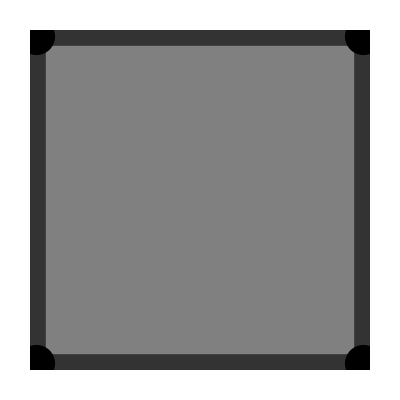

```mathematica
showCC2D[buildCC2D[{{1}}]]
```

```mathematica
cc=buildCC2D[{{1}}]
```

{{{1,1},{1,3},{3,3},{3,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2,3,4}}}

```mathematica
Dimensions[cc]⟦1⟧
```

3

```mathematica
Table[True,Dimensions[cc[[1]]][[1]]]
```

{True,True,True,True}

```mathematica
Table[True,{j,Dimensions[cc[[1]]][[1]]}]
```

```mathematica
parentNumberTable
```

{}

```mathematica
firstkillTable={}
(*parentTable={}*)
parentNumberTable={}
For[i=1,i≤Dimensions[cc][[1]],i++,
firstkillTable=Append[firstkillTable,Table[True,{j,Dimensions[cc⟦i⟧]⟦1⟧}]];
parentNumberTable=Append[parentNumberTable,Table[0,{j,Dimensions[cc⟦i⟧]⟦1⟧}]]
];
```

{}

{}

```mathematica
parentNumberTable
```

{{0,0,0,0},{0,0,0,0},{0}}

```mathematica
Dimensions[cc][[1]]
```

3

```mathematica
Dimensions[cc[[1]]][[1]]
```

4

```mathematica
(*construct parent table*)
For[i=1,i≤Dimensions[cc]⟦1⟧-1,i++,
For[j=1,j≤Dimensions[cc⟦i⟧]⟦1⟧,j++,
pNumber=0;
For[k=1,k≤Dimensions[cc⟦i+1⟧]⟦1⟧,k++,
pNumber=If[MemberQ[cc⟦i+1⟧⟦k⟧,j],pNumber+1,pNumber];
];
parentNumberTable⟦i,j⟧=pNumber;
];
];
parentNumberTable
```

{{2,2,2,2},{1,1,1,1},{0}}

```mathematica
cc
```

{{{1,1},{1,3},{3,3},{3,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2,3,4}}}

```mathematica
firstkillTable
```

{{True,True,True,True},{True,True,True,True},{True}}

```mathematica
a=getNumParent[buildCC2D[{{1}}]]
```

{{2,2,2,2},{1,1,1,1},{0}}

```mathematica
Dimensions[a[[1]]]
```

{4}

```mathematica
Table[1,{i,3},{j,i}]
```

{{1},{1,1},{1,1,1}}

```mathematica
cc
```

{{{1,1},{1,3},{3,3},{3,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2,3,4}}}

```mathematica
Table[0,{i,Dimensions[cc][[1]]},{j,Dimensions[cc⟦i⟧]⟦1⟧}]
```

{{0,0,0,0},{0,0,0,0},{0}}

```mathematica
a=getNumParent[cc]
```

{{{2,{1,2,3,4},True},{2,{1,2,3,4},False},{2,{1,2,3,4},False},{2,{1,2,3,4},False}},{{1,{1},True},{1,{1},False},{1,{1},False},{1,{1},False}},{{0,{},True}}}

```mathematica
b=getOverAllTable[cc]
```

{{False,False,False,False},{False,False,False,False},{False}}

```mathematica
a[[2,2]][[2]][[1]]
```

1

```mathematica
{{2,2,2,2},{1,1,1,1},{0}}
```

```mathematica
getEachDimension[cc]
```

{4,4,1}

```mathematica
Dimensions[cc]⟦1⟧
```

3

```mathematica
ParallelMap[If[#==1,True,False]&,a,{2}]
```

{{False,False,False,False},{True,True,True,True},{False}}

```mathematica
cc
```

{{{1,1},{1,3},{3,3},{3,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2,3,4}}}

```mathematica
cc[[1,3]]
```

{3,3}

```mathematica
Dimensions[cc][[1]]
```

3